# f.figure.rencon2.strange.baryons-all.single-if.ci-1.5.nb

```mathematica
NotebookFileName[]
```

C:\octet.formfactor\f.figure.rencon2.strange.baryons-all.single-term.ci-1.5.nb

this nb is to record the all baryon octets ge gm experiment data and calculated data.

extract the Line data, and build the band

## note

增加曲线透明度选项，这样可以隐藏曲线

## initial

## import coes

```mathematica
coe`directory=FileNameJoin[{NotebookDirectory[],"expression-coes"}]
```

C:\octet.formfactor\expression-coes

```mathematica
fucoeandmrrlnm={
FileNameJoin[{coe`directory,"fu.coeandmassrrl.consti.all.m"}],
FileNameJoin[{coe`directory,"fu.coeandmassrrl.consti.u.m"}],
FileNameJoin[{coe`directory,"fu.coeandmassrrl.consti.d.m"}],
FileNameJoin[{coe`directory,"fu.coeandmassrrl.consti.s.m"}]
};
```

```mathematica
Once[chpt`qfb`quench`coemass`masslimit=Get[FileNameJoin[{coe`directory,"chpt`qfb`quench`coemass`masslimit.m"}]]];
Once[chpt`qfa`sea`coemass`masslimit=Get[FileNameJoin[{coe`directory,"chpt`qfa`sea`coemass`masslimit.m"}]]];
Once[chpt`qfa`valence`coemass`masslimit=Get[FileNameJoin[{coe`directory,"chpt`qfa`valence`coemass`masslimit.m"}]]];
```

```mathematica
Once[
fucoeandmrrlraw=Map[Get,fucoeandmrrlnm,1]
];
```

```mathematica
Once[
fucoeandmrrl=Join[fucoeandmrrlraw,
Transpose[chpt`qfb`quench`coemass`masslimit,{2,3,1}],
Transpose[chpt`qfa`valence`coemass`masslimit,{2,3,1}],
Transpose[chpt`qfa`sea`coemass`masslimit,{2,3,1}]
]
];
```

```mathematica
fucoeandmrrlraw//Dimensions
fucoeandmrrl//Dimensions
```

{4,11,8}

{13,11,8}

```mathematica
fucoepresign={
(*+++++++++++++++++++111++++++++++++++++++++++++++++++++++++++*)
{1,1,1,
-1,(*4*)-1,(*5*)
1,1,fusign8,(*8*)fusign9,(*9*)
1,1(*11*)},
(*+++++++++++++++++++222++++++++++++++++++++++++++++++++++++++*)
{1,1,1,
-1,(*4*)-1,(*5*)
1,1,-1,(*8*)-1,(*9*)
1,1(*11*)},
(*+++++++++++++++++++333++++++++++++++++++++++++++++++++++++++*)
{1,1,1,(*3*)
-1,(*4*)-1,(*5*)
1,1,-1,(*8*)-1,(*9*)
1,1(*11*)}(*fch's sign*)
}⟦3⟧;
```

```mathematica
(*fucoeandmrrlraw [consti,figure,octet][4*11*8]*)
fucoe=Table[
Simplify[
fucoepresign*Values[fucoeandmrrl⟦seva⟧]
]
,{seva,1,13,1}
];//AbsoluteTiming
```

{0.869534,Null}

```mathematica
fumass=Keys[fucoeandmrrl];
```

```mathematica
fucoe//Dimensions
fumass//Dimensions
```

{13,11,8}

{13,11,8}

```mathematica
fucoe`simplied=Table[

Map[StringReplace[#1,"conm"->""]&,
Map[StringReplace[ToString[#1],"conm"->ToString[if]<>":",1]&,Values[fumass⟦seva,if,io⟧],{-2}]
,{-1}
]
,{seva,1,13,1}
,{if,1,11,1}
,{io,1,8,1}
];
```

```mathematica
fucoe`simplied//Dimensions
```

{13,11,8}

## import figure

{Λ, ci}→

{0.8,1.0} l1c1,{0.9,1.0} l2c1,{1.0,1.0} l3c1,

{0.8,1.5} l1c2,{0.9,1.5} l2c2,{1.0,1.5} l3c2

```mathematica
directory`fig=FileNameJoin[{NotebookDirectory[],"/expression-fig/"}]
```

C:\octet.formfactor\expression-fig

```mathematica
fig`baryons`single`term`gegm`total`origin=(
(Get[
FileNameJoin[{directory`fig,
#1
}
]
])&/@
{
(*+++++++++++++++++++++++++*)
"fig`baryons`single`term`gegm`total.L-0.90.ci-1.5.m"
}
);
```

```mathematica
fig`baryons`single`term`gegm`total`origin//Dimensions
```

fig`baryons`single`term`gegm`total`origin,{1,1,8,11,2,2},{config,seva,io,if,gegm,treeloop}

config=1;seva=1;io=1;if=1;gegm=1;treeloop=1;term=1;

## extract data

```mathematica
{data`f1[x_],data`f1[y_]}^:=data`f2[Join[x,y]]
```

```mathematica
{data`f1[x_]}^:=data`f2[x]
```

将Line中出现的数据用data`f1做tag，并且通过赋上值的方式合并到data`f2

f 是format的意思

fig`baryons`single`term`gegm`total`origin,{1,1,8,11,2,2},{config,seva,io,if,gegm,treeloop}

```mathematica
fun`data`extract[fig`calc`baryons`ge`total`origin_]:=Table[
Cases[
fig`calc`baryons`ge`total`origin⟦config,seva,io,if,gegm,treeloop,term⟧
,Line[x_]:>data`f1[x],10(*level*)
]
,{config,1,1,1}
,{seva,1,1,1}
,{io,1,8,1}
,{if,1,11,1}
,{gegm,1,2,1}
,{treeloop,1,2,1}
,{term,1,Length[fig`calc`baryons`ge`total`origin⟦config,seva,io,if,gegm,treeloop⟧],1}
]
```

```mathematica
data`baryons`single`term`gegm`total=fun`data`extract[fig`baryons`single`term`gegm`total`origin];
```

```mathematica
data`baryons`single`term`gegm`total//Dimensions
```

{1,1,8,11,2,2}

## draw

## style initial

给定线型方案, Dashing[{}] 指定线为实线

style`line`type={Dashing[{}],Dashing[{}],Dashing[{}],Dashing[Medium],Dotted,DotDashed};

选定用来绘图的数据配置

```mathematica
fontsize`frame=8;
imagesize=Scaled[.6];
```

默认的曲线间填充透明度

```mathematica
filling`opacity=Opacity[0];
```

默认线宽

Tiny,Small,Medium,Large,Larger

```mathematica
style`line`thick=Thickness[0.0025];
```

线型,Dashing[{}]指定线为实线

```mathematica
style`line`type={
(*1*)Dashing[{}],
(*2*)Dashing[Medium],
(*3*)Dotted,
(*4*)DotDashed
};
```

给定颜色方案

```mathematica
color`default = RGBColor[0.368417, 0.506779, 0.709798];
```

Red,Green,Blue,Black,White,Gray,Cyan,Magenta,Yellow,Brown,Orange,Pink,Purple,

LightRed,LightGreen,LightBlue,LightGray

LightCyan,LightMagenta,LightYellow,LightBrown,LightOrange,LightPink,LightPurple

Transparent

```mathematica
color`array={Red,Green,Blue,Black,Cyan,Magenta,Yellow,Brown,Orange,Pink,Purple};
```

设定n幅图的曲线style

```mathematica
style`line=Flatten[
Table[

Directive[
style`line`thick,
style`line`type⟦line⟧,
color`array⟦color⟧,
Opacity[1](*opacity of the curves*)
]

,{color,1,Length[color`array],1}
,{line,1,Length[style`line`type],1}
]
];
```

```mathematica
style`line//Dimensions
```

{48}

设置填充颜色和透明度

```mathematica
style`filling=Table[
{
1->{{2},Directive[filling`opacity,style`line⟦if⟧]},
3->{{2},Directive[filling`opacity,style`line⟦if⟧]}
}
,{if,1,11,1}
];
```

设置图例样式

```mathematica
style`legend=style`line;
```

设置框架样式

```mathematica
style`frame={
{
Directive[AbsoluteThickness[0.8],FontSize->fontsize`frame,Black],
Directive[AbsoluteThickness[0.8],FontSize->fontsize`frame,Black]
},
{
Directive[AbsoluteThickness[0.8],FontSize->fontsize`frame,Black],
Directive[AbsoluteThickness[0.8],FontSize->fontsize`frame,Black]
}
};
```

横纵轴线标记

```mathematica
framelabel`gegm={
{
{Style["G_E^B(Q^2)",FontFamily->"Times New Roman",FontSize->fontsize`frame],None},
{Style["Q^2(GeV^2)",FontFamily->"Times New Roman",FontSize->fontsize`frame],None}
},
{
{Style["G_M^B(Q^2)",FontFamily->"Times New Roman",FontSize->fontsize`frame],None},
{Style["Q^2(GeV^2)",FontFamily->"Times New Roman",FontSize->fontsize`frame],None}
}
};
```

## functions to draw

config=1;seva=1;io=1;if=1;gegm=1;treeloop=1;term=1;
data`baryons`single`term`gegm`total⟦config,seva,io,if,gegm,treeloop,term⟧

{1,1,8,11,2,2}

作图，并对图形的细节进行调整

```mathematica
fun`fig`gegm`cn[
data`baryons`single`term`gegm`total_,
framelabel_,(*framelabel of ge or gm*)
legend`text_,(*legend text*)
legend`ps_:legend`position,(*legend position*)
config_,seva_,io_,if_,gegm_,treeloop_,term_
]:=Legended[
(*++++++++++++++data to plot+++++++*)
ListLinePlot[
Flatten[data`baryons`single`term`gegm`total⟦config,seva,io,if,gegm,treeloop,term⟧]/.{data`f2->Sequence},
PlotStyle->style`line,
(*Filling->style`filling⟦range`if⟧,*)
PlotRange->All,
(*++++++++++++++++++++++*)
ImageSize->Large,
PlotRange->All,
PlotRangePadding->{{0,0},{Scaled[0.09],Scaled[0.09]}},
Frame->True,
FrameStyle->style`frame,
FrameLabel->framelabel⟦gegm⟧
],
(*++++++++++++++++++++++++++++++*)
Placed[
Style[
LineLegend[
style`legend⟦1;;Length[legend`text]⟧,
(Style[#1,FontFamily->"Times New Roman",FontSize->12]&)/@legend`text,
LegendLayout->"Row"
(*,LegendFunction->Framed*)
],
Magnification->fig`legend`magni
],
legend`ps
]
]
```

## fun apply

fucoe`simplied,{13,11,8},{seva,if,io}

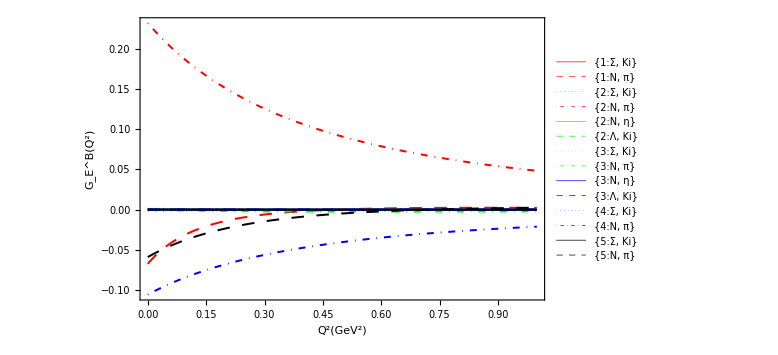

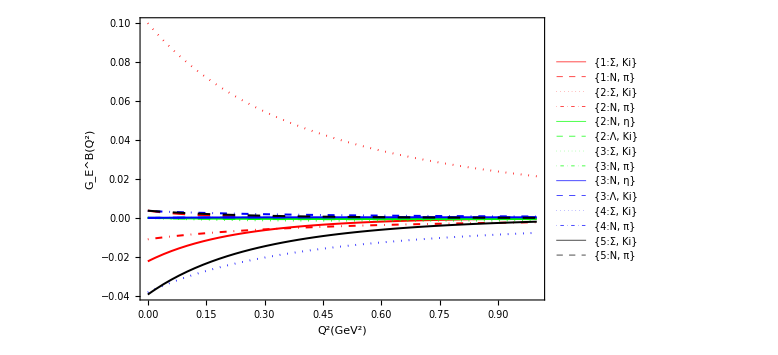

```mathematica
legend`ps=Below;
fig`legend`magni=1.5(*0.5*);
(*+++++++++++++++++++++++++*)
config=1;seva=1;io=5;if={1,2,3,4,5};gegm=1;treeloop=2;term=All;
(*+++++++++++++++++++++++++*)
legend`text=Flatten[fucoe`simplied⟦seva,if,io⟧];
(*+++++++++++++++++++++++++*)
fun`fig`gegm`cn[
data`baryons`single`term`gegm`total,
framelabel`gegm,(*framelabel of ge or gm*)
legend`text,(*legend text*)
legend`ps,(*legend position*)
config,seva,io,if,gegm,treeloop,term
]
(*++++++++++++++++++++++++*)
io=7;
(*+++++++++++++++++++++++++*)
fun`fig`gegm`cn[
data`baryons`single`term`gegm`total,
framelabel`gegm,(*framelabel of ge or gm*)
legend`text,(*legend text*)
legend`ps,(*legend position*)
config,seva,io,if,gegm,treeloop,term
]
```

## export

```mathematica
SetDirectory[FileNameJoin[{NotebookDirectory[],"/expression-results/"}]]
```

C:\octet.formfactor\expression-results

```mathematica
Export["fig`each`baryons`ge.ci-1.5.pdf",fig`each`baryons`ge];
Export["fig`each`baryons`gm.ci-1.5.pdf",fig`each`baryons`gm];
```